# Introduction to Wave Models

We have studied the phase space picture of single particle dynamics. As you have learned to think about the evolution of a paticle subject to external forces using the phase space picture, you have also been learning to use Mathematica to explore this kind of quantitative model. We are going to build on what you have learned so far in a number of diferent directions. One direction is to get out one dimensional motion and another is to break out in the much more interesting realm of systems of interacting particles. We will continue to use Mathematica to aid us in exporing these topics.

One simple generaliztion to many interacting (classical) particles is  the case of  a large system of particles held in a dynamic equilibrium configuration by interactions between each particle and its neighbors in space. Systems where the interactions between particles are only significant when the particles neighbor one another  are relatively easy to model because their behavior is simpler than what might otherwise occur where more interactions need to be taken into account. It is quite common to find systems of particles in nature held in semi-rigid stable configurations. These configurations have the properties that local disurbances from the equilibrium configuration of the particles propagate through the system. These propagating disturbances are generally referred to as ‘waves”. 

In this notebook I will lay out a simple model of inteacting particles along a line connected by ‘massless’ springs. We will use the methodologies I lay out here, and generalizations that you will invent yourself, to develop similar models of systems of particles in 2 and 3 space dimensions and also to explore the the behavior of continuous media.

TO START:  EITHER EVALUATE THE ENTIRE NOTEBOOK, (THIS WILL TAKE BETWEEN 3 and 10 MINUTES ON Most Computers)  or ALTERNATIVELY, EVALUATE AS YOU READ THROUGH THE NOTEBOOK. But make sure to evaluate all the input cells in order.

## Discrete Evolution Model

The model: Lots of little masses on a straight line,  each mass connected to its  two  neighbors by springs 

Recall that springs pull or push in proportion to their stretch or compression from their equilibrium length respectively, with a proportionality constant called the spring constant (k).

Uniform medium  : All masses the same (m) , all springs the same with the same spring constants (k), all equilibrium lengths of the springs  the same
         
omega2= k/m  - you will notice that this is the angular frequency for a simple harmonic oscillator, and sets the scale for effects of the nearest neighbor interactions
	
Δx_0 = equilibrium spacing ; we will choose  length units in which Δx_0 =1
	
We wil choose mass units in which all particle masses =1

Coming from our previous work with particles and phase space, you should imagine this as lots of little phase spaces coupled together

Here are the dynamical equations of out model. The index i refers to the ith particle, i = 1.....n number of particles.
Note: In the expression below, Δx_0 drops out of the acceleration  if the equilibrium lengths of all springs are all the same, i.e. the medium is uniform  

dx_i/dt = v_i   ;

dv_i/dt   = Force on ith particle /m =  a_i[ x_(i-1) , x_i, x_(i+1)] 
		= omega2 ( x_(i+1) -x_i -Δx_0) - omega2 (x_i -x_(i-1) -Δx_0)  
		= omega2 (  x_(i+1) + x_(i-1) - 2 x_i )

Just because I can't resist mentioning it here: it will eventually be useful to observe that     omega2 (  x_(i+1) + x_(i-1) - 2 x_i ) = ( omega2 (Δx_0)^2)   ((  x_(i+1) + x_(i-1) - 2 x_i )/(Δx_0)^2)
The first term in brackets in the last expression, omega2 (Δx_0)^2, has units of speed^2; while the second term in brackets is the discrete approximation for (ⅆ^2 ψ)/(ⅆ x^2) where ψ (x,t) is the distortion of the medium from equilibrium at position x, or perturbation of the medium. This is a little hard to visualize when the medium is constrained to 1 dimension but
not at all hard to understand when it is some other characteristic of the medium or where the medium can move more generally in space.

Models such as these require initial conditions AND boundary conditions ( in a general sense these are space-time boundary conditions...)

	Initial conditions : set all initial x_i and v_i in the phase space of  each particle

	Boundary Conditions : We will use the simplest possible boundary condtions:  x_1 and x_n(endpoints) are fixed

There are alternative boundary conditions that correspond to some different physical situations:e.g.  v is cloned at end points from nearest neighbors, or periodic boundary conditions; or even boundary conditons that correspond to something else interacting with the system  more generally at its endpoints throughout the system's evolution. We will discuss these alternatives after we have some experience with the simplest model in which we imagine the ends of our string of particles to be nailed down.

## Initialize a System State

```mathematica
initState[n_,x_,v_]:=Table[{x[i],v[i]},{i,1,n,1}];  (*initializes a state with n particles*)
omega2=1.0;  (*work in units with omega2 set to one...I have left this parameter in the rest of the development so you can play with larger or smaller omega2...this number sets the size of the interaction between adjacent particles*)

testState=initState[200,(#-100)+10Sin[2 Pi (#-100)/100]Exp[-(#-100)^2 /400]&,0*#&]; 
(*Large Distortion in space near the center and zero inital velocities, so there is a lot of stored up potential energy in the springs near the center when we start the psrticles from rest ( with zero initial velocity) at t=0*)
```

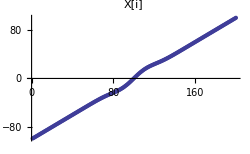
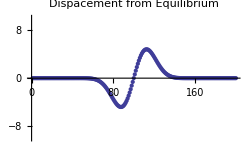
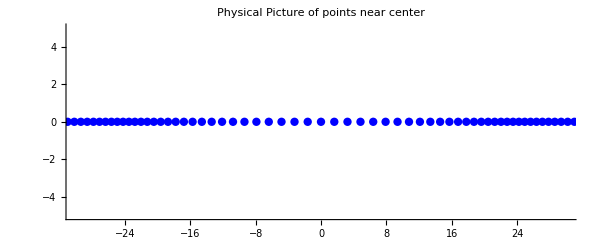
Take a look at the initial state
-Graphics--Graphics--Graphics-

```mathematica
Pane[Column[{"Take a look at the initial state",
Row[{ListPlot[Table[First[testState[[i]]],{i,1,Length[testState],1}],ImageSize->250,PlotLabel->"X[i]"],
ListPlot[Table[First[testState[[i]]]-(i-100),{i,1,Length[testState],1}],PlotRange->{-10,10},ImageSize->250,PlotLabel->"Dispacement from Equilibrium"],
Show[Graphics[{Blue,PointSize[.01],Point[testState]}],Axes->True,PlotRange->{{-30,30},{-5,5}},ImageSize->600,PlotLabel->"Physical Picture of points near center"]
}]}],Scrollbars->True]
```

```mathematica
testState[[1]]
```

{-99+(10 Sin[π/50])/ⅇ^(9801/400),0}

```mathematica
Show[Graphics[{Blue,PointSize[.01],Point[testState]}],Axes->True,PlotRange->{{-30,30},{-5,5}},ImageSize->600,PlotLabel->"Physical Picture of points near center"]
```

-Graphics-

## Step - Wise Evolution Code

### Getting Acceptable Scaling Behavior from Time Step Code

Shown below is the simplest evolution step code we could imagine using,  but if we test it we would find that energy is not conserved in the model evolution for very long - e.g. we would get
energy growing at a small but noticable rate. 
(*s is a list of lists of form {x,v}
s[[i,1]]→x
s[[i,2]]→v*)
evolveState[s_, dt_, omega2_] := Module[{n = Length[s]},
   Table[If[(i == 1) || (i == n), {s[[i, 1]], 0},(*endpoints are fixed*) {s[[i, 1]] + dt*s[[i, 2]], s[[i, 2]] + dt*omega2*(s[[i + 1, 1]] + s[[i - 1, 1]] - 2.0*s[[i, 1]])}], {i, 1, n}]];

#### We can do much better by using "2nd order code" that uses better estimates for the average acceleration and average velocity of each particle during each time step.

```mathematica
(*Use a compiled function for better computation performance in each evolution step and Code that is second order to reduce error*)
compiledf=Compile[{dt,omega2,x,v,bx,bv,ax,av},Module[{newv=v+dt*omega2*(ax+bx-2.0*x+0.5*dt*(av+bv-2.0*v))},{x+0.5*dt*(v+newv),newv}],CompilationTarget->"C"];
(*estimate the time average acceleration using an estimate for poeitions at midpoint of evolution step, evolve x with average of initial and final velocities = enforce assumption of approximately constant acceleration during time step*)
```

```mathematica
compiledf[.02,1,10,0,1,1,1,1]
```

{9.9964,-0.3596}

#### We apply our evolution step code to every particle in the system to evolve the whole system of particles forward in each time step

```mathematica
betterEvolveState[s_,dt_Real,omega2_]:=Module[{n=Length[s]},
Table[If[((i==1)||(i==n)),{s[[i,1]],0.0},compiledf[dt,omega2,s[[i,1]],s[[i,2]],s[[i-1,1]],s[[i-1,2]],s[[i+1,1]],s[[i+1,2]]]],{i,1,n,1}]];
(*Using Fixed end Boundary Conditions*)
```

### Creating a History Using NestList and Step - Wise Evolution Code

#### Applying evolution step to the whole system over and over using NestList to produce a history list of states of the system of particles:

```mathematica
betterHist[steps_,dt_,omega2_,initS_]:=NestList[
betterEvolveState[#,dt,omega2]&,initS,steps];
```

#### Generating a history with 20000 steps @ .02 time units per step for a total duration of 400 time units

```mathematica
evolutionStepCount=20000;
evolutionStepSize=0.02;
testHist=betterHist[evolutionStepCount,evolutionStepSize,omega2,testState];
```

```mathematica
testHist[[200]]
```

{{-99+(10 Sin[π/50])/ⅇ^(9801/400),0.},{-98.,2.10676×10^-10},{-97.,4.82935×10^-10},{-96.,8.91847×10^-10},{-95.,1.53094×10^-9},{-94.,2.55354×10^-9},{-93.,4.19272×10^-9},{-92.,6.79679×10^-9},{-91.,1.08889×10^-8},{-90.,1.725×10^-8},{-89.,2.70344×10^-8},{-88.,4.19305×10^-8},{-87.,6.43794×10^-8},{-86.,9.7873×10^-8},{-85.,1.47351×10^-7},{-84.,2.19717×10^-7},{-83.,3.24511×10^-7},{-82.,4.7475×10^-7},{-81.,6.87969×10^-7},{-80.,9.87464×10^-7},{-79.,1.40374×10^-6},{-78.,1.9761×10^-6},{-77.,2.75433×10^-6},{-76.,3.8002×10^-6},{-75.,5.18868×10^-6},{-74.,7.00823×10^-6},{-73.,9.35972×10^-6},{-72.,0.000012353},{-70.9999,0.0000161001},{-69.9999,0.0000207027},{-68.9999,0.0000262336},{-67.9999,0.0000327075},{-66.9998,0.0000400393},{-65.9997,0.0000479863},{-64.9997,0.0000560693},{-63.9996,0.0000634691},{-62.9995,0.0000688928},{-61.9994,0.0000704056},{-60.9993,0.0000652239},{-59.9991,0.0000494671},{-58.999,0.0000178665},{-57.9989,-0.0000365661},{-56.9989,-0.000122905},{-55.9989,-0.000252704},{-54.9991,-0.000440389},{-53.9995,-0.000703646},{-53.0001,-0.00106375},{-52.0012,-0.00154581},{-51.0029,-0.00217887},{-50.0054,-0.00299581},{-49.0089,-0.004033},{-48.0138,-0.00532959},{-47.0204,-0.00692647},{-46.0292,-0.00886468},{-45.0407,-0.0111834},{-44.0556,-0.0139174},{-43.0746,-0.0170939},{-42.0985,-0.0207288},{-41.1283,-0.0248231},{-40.1649,-0.0293581},{-39.2095,-0.0342911},{-38.2631,-0.0395516},{-37.3271,-0.0450367},{-36.4025,-0.0506087},{-35.4906,-0.0560929},{-34.5925,-0.0612774},{-33.709,-0.0659147},{-32.8411,-0.0697253},{-31.9892,-0.0724041},{-31.1536,-0.0736297},{-30.3342,-0.0730755},{-29.5302,-0.0704242},{-28.7408,-0.0653838},{-27.9641,-0.0577056},{-27.1982,-0.0472025},{-26.44,-0.0337681},{-25.6863,-0.0173932},{-24.933,0.00181817},{-24.1755,0.0236383},{-23.409,0.0477085},{-22.6279,0.0735379},{-21.8267,0.100509},{-20.9995,0.127892},{-20.1407,0.154858},{-19.2446,0.180515},{-18.3061,0.203931},{-17.3206,0.224175},{-16.2843,0.240357},{-15.1942,0.251672},{-14.0486,0.257434},{-12.8466,0.257119},{-11.5888,0.250396},{-10.2771,0.23715},{-8.91464,0.217501},{-7.50594,0.191803},{-6.05662,0.160645},{-4.5734,0.124827},{-3.06391,0.085339},{-1.5365,0.0433164},{0.,0.},{1.5365,-0.0433164},{3.06391,-0.085339},{4.5734,-0.124827},{6.05662,-0.160645},{7.50594,-0.191803},{8.91464,-0.217501},{10.2771,-0.23715},{11.5888,-0.250396},{12.8466,-0.257119},{14.0486,-0.257434},{15.1942,-0.251672},{16.2843,-0.240357},{17.3206,-0.224175},{18.3061,-0.203931},{19.2446,-0.180515},{20.1407,-0.154858},{20.9995,-0.127892},{21.8267,-0.100509},{22.6279,-0.0735379},{23.409,-0.0477085},{24.1755,-0.0236383},{24.933,-0.00181817},{25.6863,0.0173932},{26.44,0.0337681},{27.1982,0.0472025},{27.9641,0.0577056},{28.7408,0.0653838},{29.5302,0.0704242},{30.3342,0.0730755},{31.1536,0.0736297},{31.9892,0.0724041},{32.8411,0.0697253},{33.709,0.0659147},{34.5925,0.0612774},{35.4906,0.0560929},{36.4025,0.0506087},{37.3271,0.0450367},{38.2631,0.0395516},{39.2095,0.0342911},{40.1649,0.0293581},{41.1283,0.0248231},{42.0985,0.0207288},{43.0746,0.0170939},{44.0556,0.0139174},{45.0407,0.0111834},{46.0292,0.00886468},{47.0204,0.00692647},{48.0138,0.00532959},{49.0089,0.004033},{50.0054,0.00299581},{51.0029,0.00217887},{52.0012,0.00154581},{53.0001,0.00106375},{53.9995,0.000703646},{54.9991,0.000440389},{55.9989,0.000252704},{56.9989,0.000122905},{57.9989,0.0000365661},{58.999,-0.0000178665},{59.9991,-0.0000494671},{60.9993,-0.0000652239},{61.9994,-0.0000704056},{62.9995,-0.0000688928},{63.9996,-0.0000634691},{64.9997,-0.0000560693},{65.9997,-0.0000479863},{66.9998,-0.0000400393},{67.9999,-0.0000327075},{68.9999,-0.0000262336},{69.9999,-0.0000207027},{70.9999,-0.0000161001},{72.,-0.000012353},{73.,-9.35972×10^-6},{74.,-7.00823×10^-6},{75.,-5.18868×10^-6},{76.,-3.8002×10^-6},{77.,-2.75433×10^-6},{78.,-1.9761×10^-6},{79.,-1.40374×10^-6},{80.,-9.87464×10^-7},{81.,-6.87969×10^-7},{82.,-4.7475×10^-7},{83.,-3.24511×10^-7},{84.,-2.19717×10^-7},{85.,-1.47351×10^-7},{86.,-9.7873×10^-8},{87.,-6.43794×10^-8},{88.,-4.19305×10^-8},{89.,-2.70344×10^-8},{90.,-1.725×10^-8},{91.,-1.08889×10^-8},{92.,-6.79679×10^-9},{93.,-4.1928×10^-9},{94.,-2.55417×10^-9},{95.,-1.53479×10^-9},{96.,-9.07301×10^-10},{97.,-5.21005×10^-10},{98.,-2.78749×10^-10},{99.,-1.20554×10^-10},{100,0.}}

```mathematica
testHist[[1]]
```

{{-99+(10 Sin[π/50])/ⅇ^(9801/400),0},{-98+(10 Sin[π/25])/ⅇ^(2401/100),0},{-97+(10 Sin[(3 π)/50])/ⅇ^(9409/400),0},{-96+(10 Sin[(2 π)/25])/ⅇ^(576/25),0},{-95+(5 (-1+√5))/(2 ⅇ^(361/16)),0},{-94+(10 Sin[(3 π)/25])/ⅇ^(2209/100),0},{-93+(10 Sin[(7 π)/50])/ⅇ^(8649/400),0},{-92+(10 Sin[(4 π)/25])/ⅇ^(529/25),0},{-91+(10 Sin[(9 π)/50])/ⅇ^(8281/400),0},{-90+(10 √(5/8-(√5)/8))/ⅇ^(81/4),0},{-89+(10 Sin[(11 π)/50])/ⅇ^(7921/400),0},{-88+(10 Sin[(6 π)/25])/ⅇ^(484/25),0},{-87+(10 Cos[(6 π)/25])/ⅇ^(7569/400),0},{-86+(10 Cos[(11 π)/50])/ⅇ^(1849/100),0},{-85+(5 (1+√5))/(2 ⅇ^(289/16)),0},{-84+(10 Cos[(9 π)/50])/ⅇ^(441/25),0},{-83+(10 Cos[(4 π)/25])/ⅇ^(6889/400),0},{-82+(10 Cos[(7 π)/50])/ⅇ^(1681/100),0},{-81+(10 Cos[(3 π)/25])/ⅇ^(6561/400),0},{-80+(10 √(5/8+(√5)/8))/ⅇ^16,0},{-79+(10 Cos[(2 π)/25])/ⅇ^(6241/400),0},{-78+(10 Cos[(3 π)/50])/ⅇ^(1521/100),0},{-77+(10 Cos[π/25])/ⅇ^(5929/400),0},{-76+(10 Cos[π/50])/ⅇ^(361/25),0},{-75+10/ⅇ^(225/16),0},{-74+(10 Cos[π/50])/ⅇ^(1369/100),0},{-73+(10 Cos[π/25])/ⅇ^(5329/400),0},{-72+(10 Cos[(3 π)/50])/ⅇ^(324/25),0},{-71+(10 Cos[(2 π)/25])/ⅇ^(5041/400),0},{-70+(10 √(5/8+(√5)/8))/ⅇ^(49/4),0},{-69+(10 Cos[(3 π)/25])/ⅇ^(4761/400),0},{-68+(10 Cos[(7 π)/50])/ⅇ^(289/25),0},{-67+(10 Cos[(4 π)/25])/ⅇ^(4489/400),0},{-66+(10 Cos[(9 π)/50])/ⅇ^(1089/100),0},{-65+(5 (1+√5))/(2 ⅇ^(169/16)),0},{-64+(10 Cos[(11 π)/50])/ⅇ^(256/25),0},{-63+(10 Cos[(6 π)/25])/ⅇ^(3969/400),0},{-62+(10 Sin[(6 π)/25])/ⅇ^(961/100),0},{-61+(10 Sin[(11 π)/50])/ⅇ^(3721/400),0},{-60+(10 √(5/8-(√5)/8))/ⅇ^9,0},{-59+(10 Sin[(9 π)/50])/ⅇ^(3481/400),0},{-58+(10 Sin[(4 π)/25])/ⅇ^(841/100),0},{-57+(10 Sin[(7 π)/50])/ⅇ^(3249/400),0},{-56+(10 Sin[(3 π)/25])/ⅇ^(196/25),0},{-55+(5 (-1+√5))/(2 ⅇ^(121/16)),0},{-54+(10 Sin[(2 π)/25])/ⅇ^(729/100),0},{-53+(10 Sin[(3 π)/50])/ⅇ^(2809/400),0},{-52+(10 Sin[π/25])/ⅇ^(169/25),0},{-51+(10 Sin[π/50])/ⅇ^(2601/400),0},{-50,0},{-49-(10 Sin[π/50])/ⅇ^(2401/400),0},{-48-(10 Sin[π/25])/ⅇ^(144/25),0},{-47-(10 Sin[(3 π)/50])/ⅇ^(2209/400),0},{-46-(10 Sin[(2 π)/25])/ⅇ^(529/100),0},{-45+(5 (1-√5))/(2 ⅇ^(81/16)),0},{-44-(10 Sin[(3 π)/25])/ⅇ^(121/25),0},{-43-(10 Sin[(7 π)/50])/ⅇ^(1849/400),0},{-42-(10 Sin[(4 π)/25])/ⅇ^(441/100),0},{-41-(10 Sin[(9 π)/50])/ⅇ^(1681/400),0},{-40-(10 √(5/8-(√5)/8))/ⅇ^4,0},{-39-(10 Sin[(11 π)/50])/ⅇ^(1521/400),0},{-38-(10 Sin[(6 π)/25])/ⅇ^(361/100),0},{-37-(10 Cos[(6 π)/25])/ⅇ^(1369/400),0},{-36-(10 Cos[(11 π)/50])/ⅇ^(81/25),0},{-35+(5 (-1-√5))/(2 ⅇ^(49/16)),0},{-34-(10 Cos[(9 π)/50])/ⅇ^(289/100),0},{-33-(10 Cos[(4 π)/25])/ⅇ^(1089/400),0},{-32-(10 Cos[(7 π)/50])/ⅇ^(64/25),0},{-31-(10 Cos[(3 π)/25])/ⅇ^(961/400),0},{-30-(10 √(5/8+(√5)/8))/ⅇ^(9/4),0},{-29-(10 Cos[(2 π)/25])/ⅇ^(841/400),0},{-28-(10 Cos[(3 π)/50])/ⅇ^(49/25),0},{-27-(10 Cos[π/25])/ⅇ^(729/400),0},{-26-(10 Cos[π/50])/ⅇ^(169/100),0},{-25-10/ⅇ^(25/16),0},{-24-(10 Cos[π/50])/ⅇ^(36/25),0},{-23-(10 Cos[π/25])/ⅇ^(529/400),0},{-22-(10 Cos[(3 π)/50])/ⅇ^(121/100),0},{-21-(10 Cos[(2 π)/25])/ⅇ^(441/400),0},{-20-(10 √(5/8+(√5)/8))/ⅇ,0},{-19-(10 Cos[(3 π)/25])/ⅇ^(361/400),0},{-18-(10 Cos[(7 π)/50])/ⅇ^(81/100),0},{-17-(10 Cos[(4 π)/25])/ⅇ^(289/400),0},{-16-(10 Cos[(9 π)/50])/ⅇ^(16/25),0},{-15+(5 (-1-√5))/(2 ⅇ^(9/16)),0},{-14-(10 Cos[(11 π)/50])/ⅇ^(49/100),0},{-13-(10 Cos[(6 π)/25])/ⅇ^(169/400),0},{-12-(10 Sin[(6 π)/25])/ⅇ^(9/25),0},{-11-(10 Sin[(11 π)/50])/ⅇ^(121/400),0},{-10-(10 √(5/8-(√5)/8))/ⅇ^(1/4),0},{-9-(10 Sin[(9 π)/50])/ⅇ^(81/400),0},{-8-(10 Sin[(4 π)/25])/ⅇ^(4/25),0},{-7-(10 Sin[(7 π)/50])/ⅇ^(49/400),0},{-6-(10 Sin[(3 π)/25])/ⅇ^(9/100),0},{-5+(5 (1-√5))/(2 ⅇ^(1/16)),0},{-4-(10 Sin[(2 π)/25])/ⅇ^(1/25),0},{-3-(10 Sin[(3 π)/50])/ⅇ^(9/400),0},{-2-(10 Sin[π/25])/ⅇ^(1/100),0},{-1-(10 Sin[π/50])/ⅇ^(1/400),0},{0,0},{1+(10 Sin[π/50])/ⅇ^(1/400),0},{2+(10 Sin[π/25])/ⅇ^(1/100),0},{3+(10 Sin[(3 π)/50])/ⅇ^(9/400),0},{4+(10 Sin[(2 π)/25])/ⅇ^(1/25),0},{5+(5 (-1+√5))/(2 ⅇ^(1/16)),0},{6+(10 Sin[(3 π)/25])/ⅇ^(9/100),0},{7+(10 Sin[(7 π)/50])/ⅇ^(49/400),0},{8+(10 Sin[(4 π)/25])/ⅇ^(4/25),0},{9+(10 Sin[(9 π)/50])/ⅇ^(81/400),0},{10+(10 √(5/8-(√5)/8))/ⅇ^(1/4),0},{11+(10 Sin[(11 π)/50])/ⅇ^(121/400),0},{12+(10 Sin[(6 π)/25])/ⅇ^(9/25),0},{13+(10 Cos[(6 π)/25])/ⅇ^(169/400),0},{14+(10 Cos[(11 π)/50])/ⅇ^(49/100),0},{15+(5 (1+√5))/(2 ⅇ^(9/16)),0},{16+(10 Cos[(9 π)/50])/ⅇ^(16/25),0},{17+(10 Cos[(4 π)/25])/ⅇ^(289/400),0},{18+(10 Cos[(7 π)/50])/ⅇ^(81/100),0},{19+(10 Cos[(3 π)/25])/ⅇ^(361/400),0},{20+(10 √(5/8+(√5)/8))/ⅇ,0},{21+(10 Cos[(2 π)/25])/ⅇ^(441/400),0},{22+(10 Cos[(3 π)/50])/ⅇ^(121/100),0},{23+(10 Cos[π/25])/ⅇ^(529/400),0},{24+(10 Cos[π/50])/ⅇ^(36/25),0},{25+10/ⅇ^(25/16),0},{26+(10 Cos[π/50])/ⅇ^(169/100),0},{27+(10 Cos[π/25])/ⅇ^(729/400),0},{28+(10 Cos[(3 π)/50])/ⅇ^(49/25),0},{29+(10 Cos[(2 π)/25])/ⅇ^(841/400),0},{30+(10 √(5/8+(√5)/8))/ⅇ^(9/4),0},{31+(10 Cos[(3 π)/25])/ⅇ^(961/400),0},{32+(10 Cos[(7 π)/50])/ⅇ^(64/25),0},{33+(10 Cos[(4 π)/25])/ⅇ^(1089/400),0},{34+(10 Cos[(9 π)/50])/ⅇ^(289/100),0},{35+(5 (1+√5))/(2 ⅇ^(49/16)),0},{36+(10 Cos[(11 π)/50])/ⅇ^(81/25),0},{37+(10 Cos[(6 π)/25])/ⅇ^(1369/400),0},{38+(10 Sin[(6 π)/25])/ⅇ^(361/100),0},{39+(10 Sin[(11 π)/50])/ⅇ^(1521/400),0},{40+(10 √(5/8-(√5)/8))/ⅇ^4,0},{41+(10 Sin[(9 π)/50])/ⅇ^(1681/400),0},{42+(10 Sin[(4 π)/25])/ⅇ^(441/100),0},{43+(10 Sin[(7 π)/50])/ⅇ^(1849/400),0},{44+(10 Sin[(3 π)/25])/ⅇ^(121/25),0},{45+(5 (-1+√5))/(2 ⅇ^(81/16)),0},{46+(10 Sin[(2 π)/25])/ⅇ^(529/100),0},{47+(10 Sin[(3 π)/50])/ⅇ^(2209/400),0},{48+(10 Sin[π/25])/ⅇ^(144/25),0},{49+(10 Sin[π/50])/ⅇ^(2401/400),0},{50,0},{51-(10 Sin[π/50])/ⅇ^(2601/400),0},{52-(10 Sin[π/25])/ⅇ^(169/25),0},{53-(10 Sin[(3 π)/50])/ⅇ^(2809/400),0},{54-(10 Sin[(2 π)/25])/ⅇ^(729/100),0},{55+(5 (1-√5))/(2 ⅇ^(121/16)),0},{56-(10 Sin[(3 π)/25])/ⅇ^(196/25),0},{57-(10 Sin[(7 π)/50])/ⅇ^(3249/400),0},{58-(10 Sin[(4 π)/25])/ⅇ^(841/100),0},{59-(10 Sin[(9 π)/50])/ⅇ^(3481/400),0},{60-(10 √(5/8-(√5)/8))/ⅇ^9,0},{61-(10 Sin[(11 π)/50])/ⅇ^(3721/400),0},{62-(10 Sin[(6 π)/25])/ⅇ^(961/100),0},{63-(10 Cos[(6 π)/25])/ⅇ^(3969/400),0},{64-(10 Cos[(11 π)/50])/ⅇ^(256/25),0},{65+(5 (-1-√5))/(2 ⅇ^(169/16)),0},{66-(10 Cos[(9 π)/50])/ⅇ^(1089/100),0},{67-(10 Cos[(4 π)/25])/ⅇ^(4489/400),0},{68-(10 Cos[(7 π)/50])/ⅇ^(289/25),0},{69-(10 Cos[(3 π)/25])/ⅇ^(4761/400),0},{70-(10 √(5/8+(√5)/8))/ⅇ^(49/4),0},{71-(10 Cos[(2 π)/25])/ⅇ^(5041/400),0},{72-(10 Cos[(3 π)/50])/ⅇ^(324/25),0},{73-(10 Cos[π/25])/ⅇ^(5329/400),0},{74-(10 Cos[π/50])/ⅇ^(1369/100),0},{75-10/ⅇ^(225/16),0},{76-(10 Cos[π/50])/ⅇ^(361/25),0},{77-(10 Cos[π/25])/ⅇ^(5929/400),0},{78-(10 Cos[(3 π)/50])/ⅇ^(1521/100),0},{79-(10 Cos[(2 π)/25])/ⅇ^(6241/400),0},{80-(10 √(5/8+(√5)/8))/ⅇ^16,0},{81-(10 Cos[(3 π)/25])/ⅇ^(6561/400),0},{82-(10 Cos[(7 π)/50])/ⅇ^(1681/100),0},{83-(10 Cos[(4 π)/25])/ⅇ^(6889/400),0},{84-(10 Cos[(9 π)/50])/ⅇ^(441/25),0},{85+(5 (-1-√5))/(2 ⅇ^(289/16)),0},{86-(10 Cos[(11 π)/50])/ⅇ^(1849/100),0},{87-(10 Cos[(6 π)/25])/ⅇ^(7569/400),0},{88-(10 Sin[(6 π)/25])/ⅇ^(484/25),0},{89-(10 Sin[(11 π)/50])/ⅇ^(7921/400),0},{90-(10 √(5/8-(√5)/8))/ⅇ^(81/4),0},{91-(10 Sin[(9 π)/50])/ⅇ^(8281/400),0},{92-(10 Sin[(4 π)/25])/ⅇ^(529/25),0},{93-(10 Sin[(7 π)/50])/ⅇ^(8649/400),0},{94-(10 Sin[(3 π)/25])/ⅇ^(2209/100),0},{95+(5 (1-√5))/(2 ⅇ^(361/16)),0},{96-(10 Sin[(2 π)/25])/ⅇ^(576/25),0},{97-(10 Sin[(3 π)/50])/ⅇ^(9409/400),0},{98-(10 Sin[π/25])/ⅇ^(2401/100),0},{99-(10 Sin[π/50])/ⅇ^(9801/400),0},{100,0}}

```mathematica
Show[Graphics[{Blue,PointSize[.01],Point[testHist[[1]]]}],Axes->True,PlotRange->{{-30,30},{-5,5}},ImageSize->600,PlotLabel->"Physical Picture of points near center"]
```

-Graphics-

```mathematica
(*r= Table[Graphics[{Blue,PointSize[.01],Point[testHist[[i]]]}, PlotRange->{{-30,30},{-5,5}}],{i,1,1000}]*)
```

```mathematica
(*ListAnimate[r,100]*)
```

## Assessing The State of the System at an instant of time

### Functions to Assess Local and Global Properties

```mathematica
(*Displacement of Particles from Equilibrium*)
(*looks like we're assuming that the masses are 1 unit apart *)
amplitude[s_]:=Module[{n=Length[s]},Table[If[(i==1)||(i==n),{s[[i,1]],0},{s[[i,1]],s[[i,1]]-(i-100)}],{i,1,n}]];

(*Particle density*)
density[s_]:=Module[{n=Length[s]},Table[If[(i==1)||(i==n),{s[[i,1]],0},{s[[i,1]],2/(-s[[i-1,1]]+s[[i+1,1]])}],{i,1,n}]];

(*Momentum density*)
momentumDensity[s_]:=Module[{n=Length[s]},Table[If[(i==1)||(i==n),{s[[i,1]],0},{s[[i,1]],2*s[[i,2]]/(-s[[i-1,1]]+s[[i+1,1]])}],{i,1,n}]];

(*total System Momentum*)
(*add up velocities *)
sysMomentum[s_]:=Sum[s[[i,2]],{i,2,Length[s]-1}];

(*Kinetic energy Density*)
(*velocity squared over distance *)
kineticEnergyDensity[s_]:=
Module[{n=Length[s]},Table[If[(i==1)||(i==n),{s[[i,1]],0},{s[[i,1]],s[[i,2]]*s[[i,2]]/(-s[[i-1,1]]+s[[i+1,1]])}],{i,1,n}]];

(*Total System paticle energy = Kinetic energy*)
(*(1/2)mv^2 *)
sysKineticEnergy[s_]:=Sum[0.5*(s[[i,2]]^2),{i,1,Length[s]}];

(*Interaction = Potential Energy Density *)
potentialEnergyDensity[s_,omega2_]:=
Module[{n=Length[s]},Table[If[(i==1)||(i==n),{s[[i,1]],0},{s[[i,1]],(0.25*omega2(s[[i,1]]-s[[i-1,1]]-1.0)^2+0.25*omega2*(s[[i+1,1]]-s[[i,1]]-1.0)^2)/(-s[[i-1,1]]+s[[i+1,1]])}],{i,1,n}]];

(*System Potnetial Energy*)
sysPotentialEnergy[s_,omega2_]:=Sum[0.5*omega2*(s[[i,1]]-s[[i-1,1]]-1.0)^2,{i,2,Length[s]}];

totalEnergyDensity[s_,omega2_]:=Module[{tk=kineticEnergyDensity[s],tp=potentialEnergyDensity[s,omega2]},
Table[{tk[[i,1]],tk[[i,2]]+tp[[i,2]]},{i,1,Length[tk]}]
];
```

## Time Series Data for Assessement of Total System Properties

```mathematica
timeSeriesMomentum=Map[sysMomentum,testHist];
timeSeriesKineticEnergy=Map[sysKineticEnergy,testHist];
timeSeriesPotentialEnergy=Map[sysPotentialEnergy[#,omega2]&,testHist];
timeSeriesTotalEnergy=timeSeriesPotentialEnergy+timeSeriesKineticEnergy;
```

$Aborted

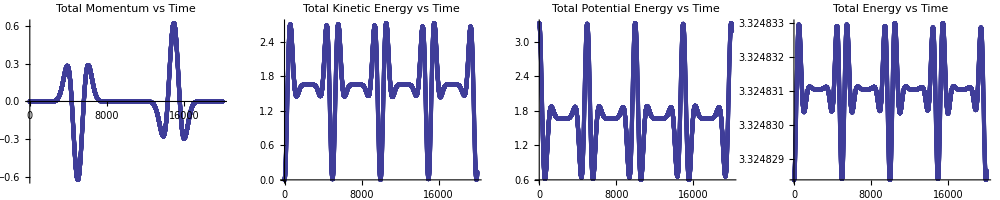

```mathematica
GraphicsRow[{ListPlot[timeSeriesMomentum,PlotLabel->"Total Momentum vs Time",PlotRange->All],ListPlot[timeSeriesKineticEnergy,PlotLabel->"Total Kinetic Energy vs Time",PlotRange->All],ListPlot[timeSeriesPotentialEnergy,PlotLabel->"Total Potential Energy vs Time" ,PlotRange->All],ListPlot[timeSeriesTotalEnergy,PlotLabel->"Total Energy vs Time",PlotRange->All]},ImageSize->{1000,200}]
(*TOTAL ENERGY: IT'S FLUCTUATING*)
```

#### Note that total energy variation is below the reported resolution of the numbers in the last graph. So our model conserves energy, at least up to 20000 steps.

## Looking at Evolving Local Properties of the System over a history

#### Evaluate all these Manipulates

```mathematica
a=Manipulate[ListLinePlot[amplitude[testHist[[i]]],PlotRange->{{-100,100},{-10,10}},PlotLabel->"Displacement from Equilibrium",AxesLabel->{"X","δX"}],{{i,1,"Time Step"},1,Length[testHist]}];
d=Manipulate[ListLinePlot[density[testHist[[i]]],PlotRange->{{-100,100},{.5,3}},PlotLabel->"Density Plot - Particles per unit length",AxesLabel->{"X","particles/length"}],{{i,1,"Time Step"},1,Length[testHist]}];
p=Manipulate[ListLinePlot[momentumDensity[testHist[[i]]],PlotRange->{{-100,100},{-.5,.5}},PlotLabel->"Linear Momentum/Unit Length"],{{i,1,"Time Step"},1,Length[testHist]}];
k=Manipulate[ListLinePlot[kineticEnergyDensity[testHist[[i]]],PlotRange->{{-100,100},{0,.2}},PlotLabel->"Kinetic Energy Density"],{{i,1,"Time Step"},1,Length[testHist]}];
u=Manipulate[ListLinePlot[potentialEnergyDensity[testHist[[i]],omega2],PlotRange->{{-100,100},{-.3,.3}},PlotLabel->"Potentila Energy Density"],{{i,1,"TimeStep"},1,Length[testHist]}];
e=Manipulate[ListLinePlot[totalEnergyDensity[testHist[[i]],omega2],PlotRange->{{-100,100},{-.25,.25}},PlotLabel->"Total Energy Densty"],{{i,1,"TmeStep"},1,Length[testHist]}];
alle=Manipulate[ListLinePlot[{totalEnergyDensity[testHist[[i]],omega2],potentialEnergyDensity[testHist[[i]],omega2],kineticEnergyDensity[testHist[[i]]]},PlotRange->{{-100,100},{-.3,.3}},PlotLabel->"Energy Densities",PlotStyle->{{Red,Thick},{Blue,Thick,Dashed},{Purple,Thick,Dashed}},PlotLegends->{"Total Energy Density","Potential Energy Density","Kinetic Energy Density"}],{{i,1,"TmeStep"},1,Length[testHist]}];
Pane[Grid[{{Style["Examining The Model","Section"],SpanFromLeft},{a,d},{p,k},{u,alle}},Alignment->Center],ImageSize->{1100,1100},Scrollbars->True]
```

Examining The Model | 
 | 
 | 
 |

## The Space - Time Picture

### Creating an interpolation function for displacement from equilibrium as a function of time = : ψ[x, t]

```mathematica
vals=Table[testHist[[i,j,1]]-(j-100),{i,1,Length[testHist],1},{j,1,200,1}];
isol=ListInterpolation[vals,{{0,400},{-100,100}},InterpolationOrder->2];
Plot3D[isol[t,x],{t,0,evolutionStepCount*evolutionStepSize},{x,-99,100},PlotRange->{-10,10},AxesLabel->{"T","X","ψ[t,x]"},PlotPoints->100]
```

-Graphics3D-

## Using NDSolve to Solve the (Continuum) Wave Equation

```mathematica
(*Woah what is this "continuum waves equation
u is displacement from equilibrium
(∂^2 u)/(∂x^2)==c^2(∂^2 u)/(∂t^2), 
ψ[0,x]==Sin[2*Pi *x/10] ⅇ^(-x^2/4)
ψ^(1,0)[0,x]==0 partial derivative with (1,0) at (0, x)
ψ[t,-10]==0 boundary!
ψ[t,10]==0 boundary!
*)
```

```mathematica
c=1.0;
ndsol=NDSolve[{D[ψ[t,x], t,t]==c^2  D[ψ[t,x], x,x],ψ[0,x]==Sin[2*Pi *x/10] ⅇ^(-x^2/4),Derivative[1,0][ψ][0,x]==0,ψ[t,-10]==0,ψ[t,10]==0},ψ,{t,0,40},{x,-10,10},StartingStepSize->.01,MaxSteps->100000]
```

{{ψ→InterpolatingFunction[{{0.,40.},{-10.,10.}},<>]}}

```mathematica
Manipulate[Plot[Evaluate[ψ[t,x]/.First[ndsol]],{x,-10,10},PlotRange->{-1,1}],{t,0.0,40.0}]
```

## The Space - Time Picture

```mathematica
Plot3D[Evaluate[ψ[t, x] /. First[ndsol]], {x, -10, 10}, {t, 0, 40}, PlotRange->{-1,1},AxesLabel -> {Style["X = Space",Larger,Bold], Style["T= Time" ,Larger,Bold], Style["u[x,t] - Disp from Equilibrium",Larger,Bold]},ImageSize->600,AspectRatio->1,PerformanceGoal->"Quality",PlotPoints->100]
```

-Graphics3D-